```mathematica
V[r_,α_,σ_,c_]:=c-α/r+σ r;
Vsb[r_,α_,σ_,c_,rsb_]:=HeavisideTheta[rsb-r](c-α/r+σ r)+HeavisideTheta[r-rsb](c-α/rsb+σ rsb);
```

```mathematica
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
Mc=1.4691897661033038;
Mb=4.882;
μc=Mc/2;
μb=Mb/2;
```

```mathematica
rsb1=r/.FindRoot[V[r,αcont[[1]],σcont[[1]],ccont[[1]]]==8/10,{r,1}]
```

6.14511

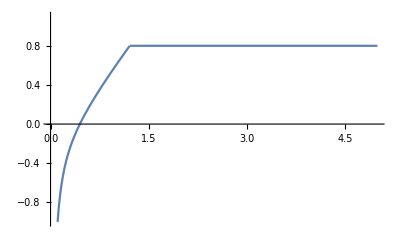

```mathematica
Plot[Vsb[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]],rsb1],{r,0,5},PlotRange->{-1,1.1}]
```

```mathematica
ccswavePDG={{3.0969,0.000006},{3.686097,0.0000025}};
ccswavePDG1={3.0969,3.686097};
```

```mathematica
ccswavemass1[rsb_]:=2Mc+NDEigenvalues[{-1/Mc Laplacian[u[x],{x}]+Vsb[x,αcont[[1]],σcont[[1]],ccont[[1]],rsb] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
rsbFinal=rsb/.Quiet[FindRoot[ccswavemass1[rsb]==ccswavePDG[[1,1]],{rsb,rsb1}]]
```

6.14511

```mathematica
rsbFinal
```

6.14511

```mathematica
ccswavemass[rsb_]:=2Mc+NDEigenvalues[{-1/Mc Laplacian[u[x],{x}]+Vsb[x,αcont[[1]],σcont[[1]],ccont[[1]],rsb] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},2,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}];
```

```mathematica
ccswavemass[rsbFinal]
```

{3.0969,3.66316}

```mathematica
2Mb + NDEigenvalues[{-1/Mb Laplacian[u[x],{x}]+Vsb[x,αcont[[1]],σcont[[1]],ccont[[1]],rsbFinal] u[x],DirichletCondition[u[x]==0,True]},u,{x,0,20},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi"}}]
```

{10.0232,9.46025,10.3551,10.5692}

```mathematica
bbswavePDG={10.02326,9.4603,10.3552,10.5794};
```

```mathematica
rsbFinal*0.197
```

1.21059